```mathematica
r= {0.4,0.1};
b={{0.05,0.1},{0.08,0.003}};
dx1[x1_,x2_]:=r[[1]] * x1 -b[[1,1]]*(x1)^2-b[[1,2]]*x1*x2;
dx2[x1_,x2_]:=-r[[2]] * x2 -b[[2,2]]*(x2)^2+b[[2,1]]*x1*x2;
cond = {x1[0]==1.0,x2[0]==4.0};
```

```mathematica
SetDirectory[NotebookDirectory[]]
data = Import["euler.dat"];
```

D:\BMSTU_coopmode_labs\Numerical_methods_6\Lab1\output

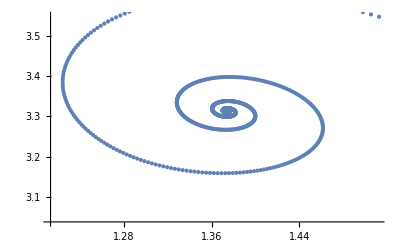

```mathematica
ListPlot[data]
```